xxz.csv

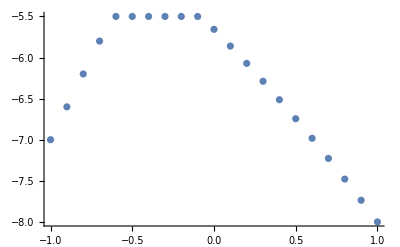

{-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
{g,J}={.75,.2};op[n_Integer,k_Integer,a_?MatrixQ]/;1≤k≤n&&Dimensions[a]=={2,2}:=KroneckerProduct[IdentityMatrix[2^(k-1),SparseArray],a,IdentityMatrix[2^(n-k),SparseArray]];
sz[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,PauliMatrix[3]];
sy[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,PauliMatrix[2]];
sx[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,PauliMatrix[1]];
HH[n_Integer/;n≥3,g_,J_]:=g*Sum[sz[n,k],{k,n}]+Sum[sx[n,k].sx[n,Mod[k+1,n,1]],{k,n}] + Sum[sy[n,k].sy[n,Mod[k+1,n,1]],{k,n}] + J*Sum[sz[n,k].sz[n,Mod[k+1,n,1]],{k,n}];
js=N@Subdivide[-1,1,20];
num =Table[J=js[[k]];kk=HH[L,g,J]//Eigenvalues//Min;{J,kk},{k,1,Length[js]}];
Export["xxz.csv",num]
ListPlot[num, PlotRange->All]
```